```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec. 3.4 lattice mismatch base on -Graphics-

## AB stacking triangle Eq. S8

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0&&r>0&&as>0&&0≤θ≤π/3&&p∈ Reals&&x∈Reals&&y∈Reals
```

R>0&&r>0&&as>0&&0≤θ≤π/3&&p∈ℝ&&x∈ℝ&&y∈ℝ

```mathematica
fAB[x_,y_,λ_]=Cos[(4 π (x-λ/√3))/(√3 λ)]+2 Cos[(2  π (x-λ/√3))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fAB[x_,y_,λ_]=fAB[x Cos[π/2]-y Sin[π/2],y Cos[π/2]+x Sin[π/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π x)/λ] Cos[(2 π (-y-λ/(√3)))/(√3 λ)]+Cos[(4 π (-y-λ/(√3)))/(√3 λ)]

```mathematica
γ=ArcCos[(Cos[θ]-p)/Sqrt[1+p^2-2p Cos[θ]]]
```

ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]

```mathematica
β=γ-θ;
```

```mathematica
ftheta[x_,y_,λ_,θ_,p_]=fAB[x Cos[-β]-y Sin[-β],y Cos[-β]+x Sin[-β],λ]  (*rotate anticlockwisely by γ-θ *)
```

Cos[(4 π (-λ/(√3)-y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)]+2 Cos[(2 π (-λ/(√3)-y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)] Cos[(2 π (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/λ]

```mathematica
λ=p Rs/(1+p^2-2 p Cos[θ])^(1/2)
(*λ is the distance between AA domain*)
```

(p Rs)/(√(1+p^2-2 p Cos[θ]))

## Rs is lattice constant of bottom layer

```mathematica
f0[x_,y_,Rs_,θ_,p_]=Simplify[ftheta[x,y,λ,θ,p]]
```

2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)] Cos[1/(3 √3 p Rs)2 π (√3 p Rs+3 y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]+Cos[1/(3 √3 p Rs)4 π (√3 p Rs+3 y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<R &&y<Sqrt[3]x+R&& y>-R/2],{x,-R,R},{y,-R,R}]
```

(3 √3 R^2)/4

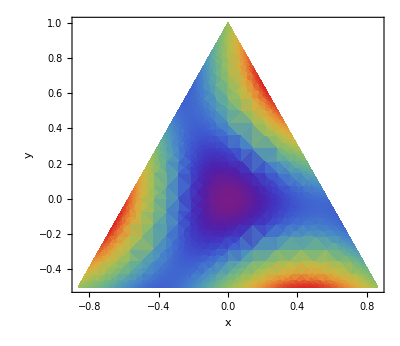

```mathematica
DensityPlot[f0[x,y,0.5,9Degree,1.3],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic]
```

## The integration progress is a little different from others

```mathematica
t1=AbsoluteTime[];
NEtri[Rs_,θ_,p_,R_]=Integrate[f0[x,y,Rs,θ,p]Boole[y+Sqrt[3]x<R &&y<Sqrt[3]x+R&& y>-R/2],{x,-R,R},{y,-R,R}] /triarea;
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

time used 9.584424123 mins

```mathematica
t1=AbsoluteTime[];
ABtri[θ_,r_,p_]=Simplify[NEtri[Rs,θ,p,Rs*p*r]] (*R=r*Rt=r*p*Rs *)
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(9 Csc[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^3 (2 Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]-(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-2 Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]-(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+√3 Sin[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+√3 Sin[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-√3 Sin[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-√3 Sin[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]))/(8 π^2 r^2 (1+p^2-2 p Cos[θ]) (√3-3 Cot[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]) (√3+3 Cot[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))

time used 0.1634897 mins

```mathematica
A[θ_,p_,r_]:=θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
```

```mathematica
B[θ_,p_,r_]:=(2 π r √(1+p^2-2 p Cos[θ]) Cos[A[θ,p,r]])/(√3)
```

```mathematica
CC[θ_,p_,r_]:=2 π r √(1+p^2-2 p Cos[θ]) Sin[A[θ,p,r]]
```

```mathematica
DD[θ_,p_,r_]:=8 π^2 r^2 (1+p^2-2 p Cos[θ]) (3-9 Cot[A[θ,p,r]]^2)
```

```mathematica
SumABtri[θ_,p_,r_]=9Csc[A[θ,p,r]]^3/DD[θ,p,r]*(2Cos[π/6+A[θ,p,r]-2B[θ,p,r]]-2Cos[π/6-A[θ,p,r]-2B[θ,p,r]]-Cos[π/6+A[θ,p,r]+B[θ,p,r]-CC[θ,p,r]]+Cos[π/6-A[θ,p,r]+B[θ,p,r]-CC[θ,p,r]]-Cos[π/6+A[θ,p,r]+B[θ,p,r]+CC[θ,p,r]]+Cos[π/6-A[θ,p,r]+B[θ,p,r]+CC[θ,p,r]]+√3 Sin[π/6+A[θ,p,r]+B[θ,p,r]-CC[θ,p,r]]+√3 Sin[π/6-A[θ,p,r]+B[θ,p,r]-CC[θ,p,r]]-√3 Sin[π/6+A[θ,p,r]+B[θ,p,r]+CC[θ,p,r]]-√3 Sin[π/6-A[θ,p,r]+B[θ,p,r]+CC[θ,p,r]])
```

(9 Csc[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^3 (2 Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]-(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-2 Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]-(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-Cos[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+Cos[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+√3 Sin[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+√3 Sin[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)-2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-√3 Sin[π/6+θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-√3 Sin[π/6-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]+(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]))/(8 π^2 r^2 (1+p^2-2 p Cos[θ]) (3-9 Cot[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^2))

```mathematica
ToMatlab[ABtri[theta,r,p]]
```

(9/8).*pi.^(-2).*r.^(-2).*(1+p.^2+(-2).*p.*cos(theta)).^(-1).*( ...
  3.^(1/2)+(-3).*cot(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+ ...
  (-2).*p.*cos(theta)).^(-1/2)))).^(-1).*(3.^(1/2)+3.*cot(theta+(-1) ...
  .*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)) ...
  )).^(-1).*csc(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2) ...
  .*p.*cos(theta)).^(-1/2))).^3.*(2.*cos((1/6).*pi+theta+(-1).*acos( ...
  ((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+(-4).* ...
  3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*cos(theta+( ...
  -1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^( ...
  -1/2))))+(-2).*cos((1/6).*pi+(-1).*theta+acos(((-1).*p+cos(theta)) ...
  .*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+(-4).*3.^(-1/2).*pi.*r.*( ...
  1+p.^2+(-2).*p.*cos(theta)).^(1/2).*cos(theta+(-1).*acos(((-1).*p+ ...
  cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))))+(-1).*cos(( ...
  1/6).*pi+theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(-1/2))+2.*3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos( ...
  theta)).^(1/2).*cos(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(-1/2)))+(-2).*pi.*r.*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(1/2).*sin(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(-1/2))))+cos((1/6).*pi+(-1).*theta+ ...
  acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+ ...
  2.*3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*cos( ...
  theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta) ...
  ).^(-1/2)))+(-2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*sin( ...
  theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta) ...
  ).^(-1/2))))+(-1).*cos((1/6).*pi+theta+(-1).*acos(((-1).*p+cos( ...
  theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+2.*3.^(-1/2).*pi.* ...
  r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*cos(theta+(-1).*acos(((-1) ...
  .*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)))+2.*pi.*r.* ...
  (1+p.^2+(-2).*p.*cos(theta)).^(1/2).*sin(theta+(-1).*acos(((-1).* ...
  p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))))+cos((1/6).* ...
  pi+(-1).*theta+acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos( ...
  theta)).^(-1/2))+2.*3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)) ...
  .^(1/2).*cos(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).* ...
  p.*cos(theta)).^(-1/2)))+2.*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^( ...
  1/2).*sin(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(-1/2))))+3.^(1/2).*sin((1/6).*pi+theta+(-1).*acos((( ...
  -1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+2.*3.^( ...
  -1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*cos(theta+(-1) ...
  .*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)) ...
  )+(-2).*pi.*r.*(1+p.^2+(-2).*p.*cos(theta)).^(1/2).*sin(theta+(-1) ...
  .*acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)) ...
  ))+3.^(1/2).*sin((1/6).*pi+(-1).*theta+acos(((-1).*p+cos(theta)).* ...
  (1+p.^2+(-2).*p.*cos(theta)).^(-1/2))+2.*3.^(-1/2).*pi.*r.*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(1/2).*cos(theta+(-1).*acos(((-1).*p+ ...
  cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)))+(-2).*pi.*r.*( ...
  1+p.^2+(-2).*p.*cos(theta)).^(1/2).*sin(theta+(-1).*acos(((-1).*p+ ...
  cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))))+(-1).*3.^( ...
  1/2).*sin((1/6).*pi+theta+(-1).*acos(((-1).*p+cos(theta)).*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(-1/2))+2.*3.^(-1/2).*pi.*r.*(1+p.^2+( ...
  -2).*p.*cos(theta)).^(1/2).*cos(theta+(-1).*acos(((-1).*p+cos( ...
  theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)))+2.*pi.*r.*(1+p.^2+ ...
  (-2).*p.*cos(theta)).^(1/2).*sin(theta+(-1).*acos(((-1).*p+cos( ...
  theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2))))+(-1).*3.^(1/2).* ...
  sin((1/6).*pi+(-1).*theta+acos(((-1).*p+cos(theta)).*(1+p.^2+(-2) ...
  .*p.*cos(theta)).^(-1/2))+2.*3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(1/2).*cos(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(-1/2)))+2.*pi.*r.*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(1/2).*sin(theta+(-1).*acos(((-1).*p+cos(theta)).*(1+ ...
  p.^2+(-2).*p.*cos(theta)).^(-1/2)))));